```mathematica
(*This routine is very important. It rotates L vector around S = S1+S2, while keeping S1, S2 constants. This keeps the egg in Fig. 2 of Gerosa the same while changing ξ (constant of motion), thus changing morphology.*)RotateVectorAroundAxis[L_,S_,phi_]:=Module[{SUnit,LParallel,LPerpendicular,RotationMatrix,LFinal},(*Step 1:Normalize the S vector*)SUnit=Normalize[S];
(*Step 2:Decompose L into parallel and perpendicular components*)LParallel=(L.SUnit) SUnit;
LPerpendicular=L-LParallel;
(*Step 3:Construct the rotation matrix around the axis SUnit by angle phi*)RotationMatrix=RotationTransform[phi,SUnit];
(*Step 4:Rotate the perpendicular component*)LFinal=LParallel+RotationMatrix[LPerpendicular];
(*Output the final rotated vector*)LFinal];
```

```mathematica
(*m2 < m1 in Gerosa. q of Gerosa is 1/q of Racine.*)
```

```mathematica
m1 = 3.3;
m2 =2.3; 
S1init= {-2,5,3} ;
S2init =2  S1init  +-2 {2,1,0};
Linit0 = S2init  + {1,3,1} ;
Sinit=S1init + S2init; 
phiRotationAngle=3.371709796270106  -(1) 0.001     (*The first term alone (without the small perturbation term) keeps us on the supposed "separatrix". The perturbation term kicks us off the "separatrix". *)   ;
Linit=RotateVectorAroundAxis[Linit0,Sinit,phiRotationAngle];


end = 1;
d=1;

M=m1+m2;
μ =  (m1 m2)/M ;
q = m1/m2 ;
S0= (1+m2/m1)S1[t]+(1+m1/m2)S2[t] ;
S = S1[t]+S2[t];
λ = ((1+m2/m1)L[t].S1[t]+(1+m1/m2)L[t].S2[t])/Norm[L[t]]^2;

sol1 = NDSolve[{S1'[t]==1/(2 d^3) Cross[(4 + 3 m2/m1 - 3 μ/m1 λ )L[t]+S2[t], S1[t]] ,S2'[t]==1/(2 d^3) Cross[(4 + 3 m1/m2 - 3 μ/m2 λ )L[t]+S1[t], S2[t]],
L'[t]==1/(2 d^3) Cross[ S +3 (1-μ/M λ)S0, L[t]]
, S1[0]==S1init , S2[0]==S2init,  L[0]==Linit},  {S1,S2,L},{t,0,end}];
```

```mathematica
S1=(S1 /.sol1[[1]])  ;
S2=(S2 /.sol1[[1]])   ;
L=(L /.sol1[[1]])  ;
```

```mathematica
J = L[t]+S1[t]+S2[t];
zcap = J/Norm[J]  ; 
(*Plot[zcap , {t,0,end}]      *) (*This is z_cap*)
```

```mathematica
xcap = (L[t]-zcap.L[t]  zcap)/Norm[L[t]-zcap.L[t]  zcap];   (*This is x_cap*)
(*Plot[  xcap, {t,0,end}]*)
```

```mathematica
ycap = Cross[zcap,xcap];
(*Plot[  ycap  //Norm, {t,0,end}]  *)
```

```mathematica
Sperp = Cross[ycap,  S1[t]+S2[t]] ; 
SperpNorm = Sperp/Norm[Sperp] ; 
S1norm = S1[t]/Norm[S1[t]] ;
Snorm = S/Norm[S] ;
```

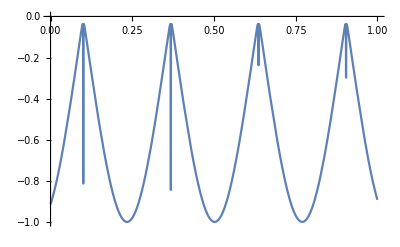

```mathematica
Plot[ (S1norm.SperpNorm)/Norm[Cross[S1norm, Snorm]] ,{t,0,end}]
```

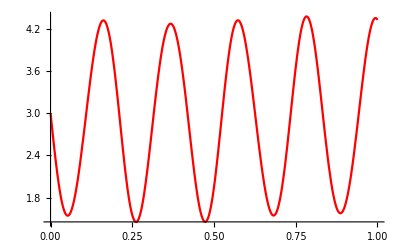

```mathematica
Plot[ (S1[t])[[3]] ,{t,0,end}, PlotStyle->Red]
```

```mathematica
AllThreePhasesPossible=(Linit+S1init+S2init //Norm )> (S1init//Norm)+(S2init//Norm)-(Linit//Norm);
ξTestFunc[phiRotationAngle_] := M^-2((1+q^-1)S1init+(1+q)S2init).(RotateVectorAroundAxis[Linit0,Sinit,phiRotationAngle])/Norm[RotateVectorAroundAxis[Linit0,Sinit,phiRotationAngle]]
```

```mathematica
Smin = Max[Abs[(Linit+S1init+S2init //Norm )-( Linit//Norm)],
Abs[(S1init //Norm )-( S2init//Norm)]  ]  //N ;
Smax = Min[(Linit+S1init+S2init //Norm )+( Linit//Norm)   //N,
(S1init //Norm )+( S2init//Norm)   //N] ;
```

```mathematica
Clear[J,L,S,S1,S2];
```

1.31008

1.28205

1.31008

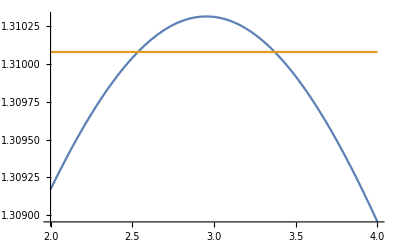

{x→3.37171}

```mathematica
A1 = (J^2 - (L-S)^2)^(1/2)      ;
A2 = (-J^2 + (L+S)^2)^(1/2)    ;
A3 = (S^2 - (S1-S2)^2)^(1/2)  ;
A4 = ((S1+S2)^2-S^2)^(1/2)    ;
ξPlus = ((J^2-L^2-S^2)(S^2(1+q^-1)^2-(S1^2-S2^2)(1-q^-2))+ (1-q^-2)A1 A2 A3 A4)/(4 q^-1 M^2 S^2 L)   ;

S1= S1init;
S2 =S2init;
L =Linit ;
(*S = S1+S2 ;*)
J = S1init+S2init+Linit;
S1 = S1//Norm;
S2 = S2 //Norm;
(*S = S //Norm ;*)
L = L //Norm;
J=J//Norm;

ξ1   =ξPlus  /.S ->Smin     //Re
ξ2   =ξPlus  /.S ->Smax    //Re
ξTest=ξTestFunc[phiRotationAngle]
Plot[{ξTestFunc[x],ξ1(*,ξ2*)} , {x,2,4}]
FindRoot[ξTestFunc[x] - ξ1 ,{x,0,0,4}]      (*This root-finding finds the rotation angle which lands us on the "separatrix"*)
```

```mathematica
AllThreePhasesPossible
If[AllThreePhasesPossible,
If[ξTest>Max[ξ1,ξ2],
Decision = AroundPi];
If[ξTest<Min[ξ1,ξ2],
Decision = Around0];
If[ξTest>Min[ξ1,ξ2] &&ξTest<Max[ξ1,ξ2],
Decision = AllTheWay];
]
Decision
```

True

AroundPi

```mathematica
Quit[];
```

3